Номер 2
Условие:
а) Вычислить с помощью формулы второго порядка точности и составить таблицу приближенных значений y'_i производной функции f(x) на отрезке [-1, 3] с шагом h = 0,2;
б)  Изобразить на одном чертеже (на отрезке [-1, 3]) график функции f' (x), полученной с помощью функции D пакета Mathematica, и точки (x_i,y'_i) , соответствующие приближенным значениям производной, найденные в пункте а.

a) 
Введем функцию f (x), отрезок и шаг.

```mathematica
f[x_]=(√(1+x^3))/(Sin[7x+1])^2;a=-0.8(*Взял другое значение из-за появления комплексных корней.*); b=3; h = 0.2;
```

Вычислим количество значений производной на отрезке [-1, 3] с шагом h = 0,2.

```mathematica
n=(b-a)/h;
```

Формула второго порядка точности:

```mathematica
pro1 [x_] = (f[x+h]-f[x-h])/(2h);
```

Составим таблицу:

```mathematica
Table[{a+h*i,pro1[a+h*i]},{i,0,n}]
```

{{-0.8,649.616},{-0.6,0.781656},{-0.4,-633.197},{-0.2,0.98038},{0.,-10.9183},{0.2,3.35756},{0.4,-1.96918},{0.6,24.7844},{0.8,0.079858},{1.,6695.3},{1.2,1.4152},{1.4,-6683.},{1.6,3.82526},{1.8,-26.2419},{2.,12.1021},{2.2,-4.93659},{2.4,70.4632},{2.6,-0.427103},{2.8,168760.},{3.,2.54325}}

б)

```mathematica
dif[x_]=D[f[x],x];
```

Нарисуем график производной, точки, которые мы высчитали с помощью функции D пакета Mathematica, точки, соответствующие приближенным значениям производной.

```mathematica
graphic1 = Plot[dif[x],{x,a,b},PlotRange->{{-1,3}, {-100, 100}}];
graphic2 = ListPlot[Table[{a+h*i,dif[a+h*i]},{i,0,n}], PlotStyle->Red];
graphic3 = ListPlot[Table[{a+h*i,pro1[a+h*i]},{i,0,n}], PlotStyle->Green];
```

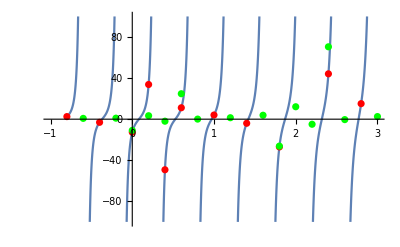

```mathematica
Show[graphic1, graphic2, graphic3]
```